```mathematica
num[c_]:=Numerator[c];den[c_]:=Denominator[c]
alpha[n_,c_]:=alpha[n,c]=den[c] (Floor[n/den[c]]-Floor[(n-1)/den[c]])-num[c] (Floor[n/num[c]]-Floor[(n-1)/num[c]])
Lm1[ n_, c_ ] := (1/den[c])Sum[If[alpha[j,c]==0,0,alpha[j,c]( Log[j/den[c]]-Lm1[den[c] n/j,c])],{j,den[c]+1,den[c] n}]
Em1[ n_, c_ ] := 1-(1/den[c])Sum[If[alpha[j,c]==0,0,alpha[j,c]( Em1[den[c] n/j,c])],{j,den[c]+1,den[c] n}]
L1mAlt[ n_, c_] := den[c]^-1 Sum[ Em1[ n den[c]/j, c ]N[alpha[ j, c]Log[j/den[c]]],{j,1,n den[c]}]
```

```mathematica
{L1mAlt[20, 3/2],N[ Lm1[20,3/2]]}
```

{-0.301201,-0.301201}

```mathematica
{N[E1[ 88, -1, 3/2]], N[ Em1[88,3/2]]}
```

{E1[88.,-1.,1.5],31.8931}

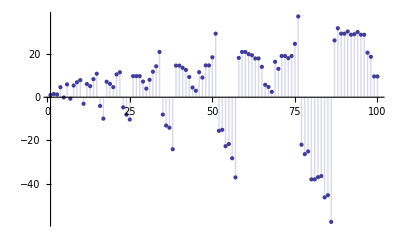

```mathematica
DiscretePlot[ Em1[ n, 3/2],{n,1,100}]
```